```mathematica
oddTriangles[basis,initialConditions1D]
```

{{FaceForm[GrayLevel[1]],EdgeForm[GrayLevel[0]],Triangle[{{0,0},{1,0},{0.5,(√3)/2}}]},{FaceForm[GrayLevel[1]],EdgeForm[GrayLevel[0]],Triangle[{{1,0},{2,0},{1.5,(√3)/2}}]},{FaceForm[GrayLevel[1]],EdgeForm[GrayLevel[0]],Triangle[{{2,0},{3,0},{2.5,(√3)/2}}]},{FaceForm[GrayLevel[1]],EdgeForm[GrayLevel[0]],Triangle[{{3,0},{4,0},{3.5,(√3)/2}}]},{FaceForm[GrayLevel[1]],EdgeForm[GrayLevel[0]],Triangle[{{4,0},{5,0},{4.5,(√3)/2}}]},{FaceForm[GrayLevel[1]],EdgeForm[GrayLevel[0]],Triangle[{{5,0},{6,0},{5.5,(√3)/2}}]},{FaceForm[GrayLevel[1]],EdgeForm[GrayLevel[0]],Triangle[{{6,0},{7,0},{6.5,(√3)/2}}]},{FaceForm[GrayLevel[1]],EdgeForm[GrayLevel[0]],Triangle[{{7,0},{8,0},{7.5,(√3)/2}}]}}

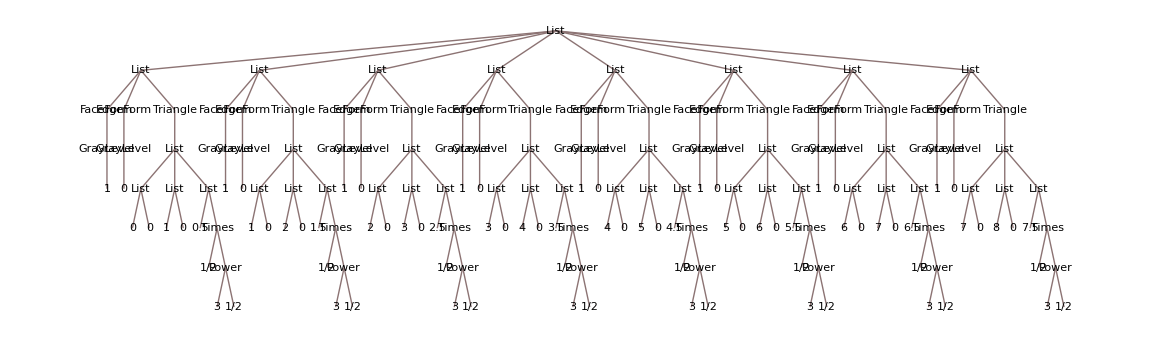

```mathematica
TreeForm[%]
```

```mathematica
Dimensions@evenTriangleCells[basis,initialConditions2D]
```

{5,3,3}

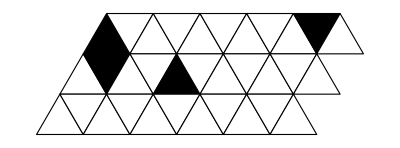

{11,3,3}

```mathematica
Graphics[Riffle[o,e]]
Dimensions[Riffle[o,e]]
```

```mathematica
triangleCells[basis,initialConditions2D][[5,2]]
```

{FaceForm[GrayLevel[0]],EdgeForm[GrayLevel[0]],Triangle[{{2.5,(√3)/2},{3.5,(√3)/2},{3.,√3}}]}

```mathematica
initialConditions2D//Dimensions
```

{3,11}

```mathematica
vonNeumannNeighborhood[cell_,state_]:=Module[{y=cell[[1]],x=cell[[2]],flipped=Reverse[state,1]},
If[OddQ[x],
<|cell->{Check[flipped[[y+1,x+1]],0],Check[flipped[[y-1,x]],0],Check[flipped[[y+1,x]],0]}|>,
<|cell->{}|>
]
];
```

```mathematica
vonNeumannNeighborhood[{1,1},initialConditions2D]
```

Part::partd1: Depth of object SparseArray[Automatic,{3,11},0,{1,{{0,1,3,4},{{10},{5},{2},{1}}},{1,1,1,1}}]⟦0,1⟧ is not sufficient for the given part specification.

Part::partd1: Depth of object {{0,0,0,0,0,0,0,0,0,1,0},{0,1,0,0,1,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0}} is not sufficient for the given part specification.

<|{1,1}→{1,0,0}|>

```mathematica
initialConditions2D//MatrixForm
initialConditions2D[[1,1]]
initialConditions2D[[2,5]]
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0)

1

1

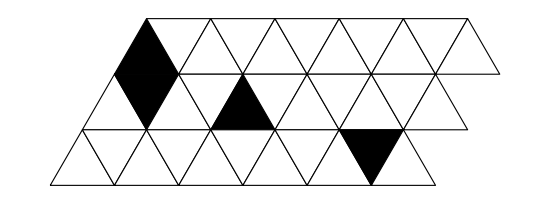

```mathematica
initialConditions2D[[2,2]]=1;
triangleCellPlot[basis,initialConditions2D]
```

```mathematica
(test=Table[{i,j,GrayLevel[RandomInteger[]]},{i,1,3},{j,1,3}])//MatrixForm
test[[2,1]]
```

((1
1
GrayLevel[0]) | (1
2
GrayLevel[1]) | (1
3
GrayLevel[0])
(2
1
GrayLevel[0]) | (2
2
GrayLevel[0]) | (2
3
GrayLevel[1])
(3
1
GrayLevel[1]) | (3
2
GrayLevel[0]) | (3
3
GrayLevel[0]))

{2,1,GrayLevel[0]}

```mathematica
vNN[cell_,lattice_]:=Module[{x=cell[[1]],y=cell[[2]]},
<|cell->{lattice[[x,y-1]],lattice[[x-1,y]],lattice[[x,y]],lattice[[x+1,y]],lattice[[x,y+1]]}|>
];
```

```mathematica
nbhds=vNN[{2,1},test]
```

<|{2,1}→{List,{1,1,GrayLevel[0]},{2,1,GrayLevel[0]},{3,1,GrayLevel[1]},{2,2,GrayLevel[0]}}|>

```mathematica
currentState[cell_,lattice_]:=lattice
```

{2,2}

```mathematica
test[[3,1,{1,2}]]
```

{3,1}

```mathematica
Lookup[nbhds,{{2,1}}]
```

{{List,{1,1,GrayLevel[0]},{2,1,GrayLevel[0]},{3,1,GrayLevel[1]},{2,2,GrayLevel[0]}}}

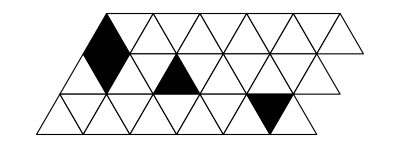

```mathematica
Graphics[t=triangleCells[basis,initialConditions2D]]
```

```mathematica
t[[1,1]]
```

{FaceForm[GrayLevel[1]],EdgeForm[GrayLevel[0]],Triangle[{{0.,0},{1.,0},{0.5,(√3)/2}}]}

```mathematica
initialConditions2D//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0)